```mathematica
Arms[x1_,x2_,x3_,x4_]:=FindRoot[
{Sum[Cos[Subscript[θ, i]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]],{i,1,4}]==0,
Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,4}]==0},
{{Subscript[θ, 1],x1},{Subscript[θ, 2],x2},{Subscript[θ, 3],x3},{Subscript[θ, 4],x4}},
MaxIterations->1000]
TraceOut[t_]:=FindRoot[
{2 Sum[Cos[Subscript[θ, i]],{i,1,2}]==2.5+Cos[t],
2 Sum[Sin[Subscript[θ, i]],{i,1,2}]==3 + Sin[t]},
{{Subscript[θ, 1],1},{Subscript[θ, 2],0.5}}
]
```

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.07420;Subscript[δ, 3]=-0.04497;Subscript[δ, 4]=-0.00179;
sol=Arms[3,1,2,1] (*Set 1*)
```

{θ_1→1.88484,θ_2→0.628205,θ_3→5.65487,θ_4→-1.88514}

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.02742;Subscript[δ, 3]=0.02853;Subscript[δ, 4]=-0.07487;
sol=Arms[2,1,6,4] (*Set 2 Works!*)
```

{θ_1→1.8849,θ_2→0.628398,θ_3→5.65479,θ_4→4.39828}

```mathematica
Subscript[δ, 1]=-0.02412;Subscript[δ, 2]=-0.16026;Subscript[δ, 3]=0.27843;Subscript[δ, 4]=-0.27794;
sol=Arms[2,0.5,6,4] (*Set 3*)
```

{θ_1→1.88503,θ_2→0.628328,θ_3→5.6549,θ_4→4.39828}

```mathematica
Subscript[δ, 1]=0.07272;Subscript[δ, 2]=1.20678;Subscript[δ, 3]=4.78410;Subscript[δ, 4]=1.3022;
sol=Arms[2,0.5,6,4] (*Set 4 Works!*)
```

{θ_1→1.06552,θ_2→-0.982549,θ_3→5.51952,θ_4→2.43605}

```mathematica
Subscript[δ, 1]=-0.71895;Subscript[δ, 2]=0.71895;Subscript[δ, 3]=-0.52670;Subscript[δ, 4]=-0.15747;
sol=Arms[2,0.5,6,4] (*Set 5*)
```

{θ_1→1.11641,θ_2→0.261798,θ_3→5.28677,θ_4→3.46502}

{{0,0},{-0.309084,0.951035},{0.499928,1.53883},{1.30897,0.951073},{1.,3.33067×10^-16}}

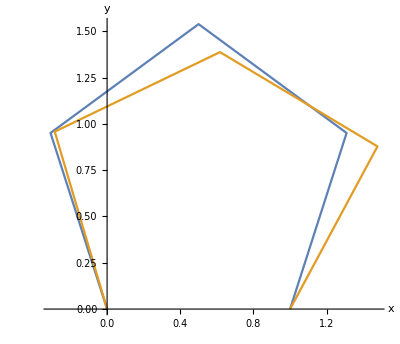

```mathematica
start = Prepend[Table[{Sum[Cos[Subscript[θ, i]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
end = Prepend[Table[{Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
ListPlot[{start,end}, Joined->True,AspectRatio->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
m = Table[i π/7,{i,1,4}];
Table[{Sum[-Cos[m[[i]]+0.2 t^2 i],{i,1,n}],Sum[Sin[m[[i]]+0.2 t^2 i],{i,1,n}]},{n,1,4}]
```

{{-Cos[π/7+0.2 t^2],Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[π/14-0.6 t^2]+Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6 t^2]-Sin[(3 π)/14-0.4 t^2]+Sin[π/14+0.8 t^2],Cos[π/14-0.6 t^2]+Cos[(3 π)/14-0.4 t^2]+Cos[π/14+0.8 t^2]+Sin[π/7+0.2 t^2]}}

```mathematica
anim=Animate[ListPlot[{{0,0},{-Cos[π/7+0.2 t^2],Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6000000000000001 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[π/14-0.6000000000000001 t^2]+Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6000000000000001 t^2]-Sin[(3 π)/14-0.4 t^2]+Sin[π/14+0.8 t^2],Cos[π/14-0.6000000000000001 t^2]+Cos[(3 π)/14-0.4 t^2]+Cos[π/14+0.8 t^2]+Sin[π/7+0.2 t^2]}},Joined->True,PlotRange->{{-2,2},{0,4}},AspectRatio->1],{t,2,0},AnimationDirection->ForwardBackward,ControlType->None]
```

```mathematica
Export["Anim2.gif",anim]
```

Anim2.gif

```mathematica
a=Animate[sol=TraceOut[t];
start = Prepend[Table[{2Sum[Cos[Subscript[θ, i]]/.sol,{i,1,n}],2Sum[Sin[Subscript[θ, i]]/.sol,{i,1,n}]},{n,1,2}],{0,0}];
Show[ListPlot[{start}, Joined->True,AspectRatio->Equal,AxesLabel->{"x","y"},PlotRange->{{-1,4},{0,4}},PlotStyle->Blue],ParametricPlot[{{2.5t,3t},{(2.5+Cos[26π/32])t,(3+Sin[26π/32])t}},{t,0,1},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}],Graphics[{Red,Opacity[0.25],EdgeForm[{Red,Thick}],Disk[{2.5,3}]}]],{t,26π/32,π+ArcTan[6/5]},AnimationDirection->ForwardBackward]
```

```mathematica
Export["Nice.gif",a,AnimationRepetitions->Infinity]
```

Nice.gif

```mathematica
(*Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.07420;Subscript[δ, 3]=-0.04497;Subscript[δ, 4]=-0.00179;*)
(*Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.02742;Subscript[δ, 3]=0.02853;Subscript[δ, 4]=-0.07487;*)
(*Subscript[δ, 1]=-0.02412;Subscript[δ, 2]=-0.16026;Subscript[δ, 3]=0.27843;Subscript[δ, 4]=-0.27794;*)
(*Subscript[δ, 1]=-0.07272;Subscript[δ, 2]=-1.20678;Subscript[δ, 3]=-4.78410;Subscript[δ, 4]=-1.3022;*)
(*Subscript[δ, 1]=-0.71895;Subscript[δ, 2]=0.71895;Subscript[δ, 3]=-0.52670;Subscript[δ, 4]=-0.15747;*)
Subscript[θ, 1]=3π/5;Subscript[θ, 2]=1π/5;Subscript[θ, 3]=9π/5;Subscript[θ, 4]=7π/5;
```

{{0,0},{1/4 (1-√5),√(5/8+(√5)/8)},{1/4 (1-√5)+1/4 (1+√5),√(5/8-(√5)/8)+√(5/8+(√5)/8)},{1/4 (1-√5)+1/2 (1+√5),√(5/8+(√5)/8)},{1/2 (1-√5)+1/2 (1+√5),0}}

{{0,0},{-0.2391,0.970995},{0.556268,0.364868},{1.47389,-0.0325789},{0.488997,-0.205724}}

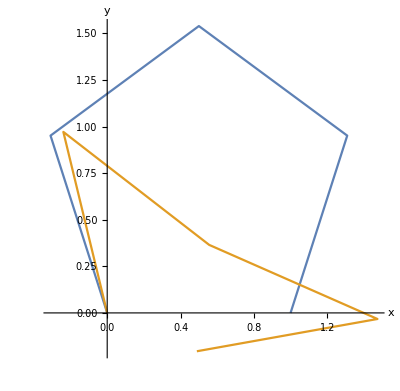

```mathematica
start = Prepend[Table[{Sum[Cos[Subscript[θ, i]],{i,1,n}],Sum[Sin[Subscript[θ, i]],{i,1,n}]},{n,1,4}],{0,0}]
end = Prepend[Table[{Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,n}],Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,n}]},{n,1,4}],{0,0}]
ListPlot[{start,end}, Joined->True,AspectRatio->Automatic,AxesLabel->{"x","y"}]
```